```mathematica
Clear[a]
```

```mathematica
f0[x_,a_]=Exp[-a^2x^2]
```

ⅇ^(-a^2 x^2)

```mathematica
f[x_,a_]=f0[x,a]/Integrate[f0[x,a],{x,0,1}]
```

(2 a ⅇ^(-a^2 x^2))/(√π Erf[a])

```mathematica
df[x_,a_]=D[f[x,a],x]
```

-(4 a^3 ⅇ^(-a^2 x^2) x)/(√π Erf[a])

```mathematica
normdf[a_,h_]=Integrate[-df[x,a],{x,0,h}]
```

-(2 a (-1+ⅇ^(-a^2 h^2)))/(√π Erf[a])

```mathematica
d2f[x_,a_]=Simplify[D[df[x,a],x]]
```

(4 a^3 ⅇ^(-a^2 x^2) (-1+2 a^2 x^2))/(√π Erf[a])

```mathematica
normd2f[a_,h_]=Simplify[Integrate[-d2f[x,a],{x,0,Min[h,1/(Sqrt[2]a)]}]+Integrate[d2f[x,a],{x,Min[h,1/(Sqrt[2]a)],h}]]
```

-(4 a^3 (ⅇ^(-a^2 h^2) h-2 ⅇ^(-a^2 Min[1/(√2 a),h]^2) Min[1/(√2 a),h]))/(√π Erf[a])

```mathematica
a=10
```

10

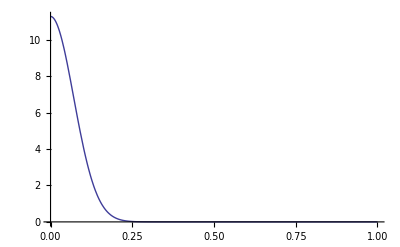

```mathematica
Plot[f[x,a],{x,0,1},AxesOrigin->{0,0}, PlotRange -> Full]
```

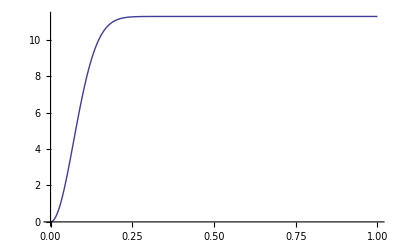

```mathematica
Plot[normdf[a,h],{h,0,1},AxesOrigin->{0,0}]
```

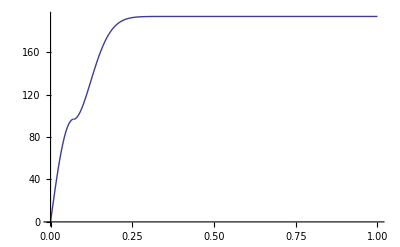

```mathematica
Plot[normd2f[a,h],{h,0,1},AxesOrigin->{0,0}]
```

```mathematica
tau[h_]= 17+2/h
```

17+2/h

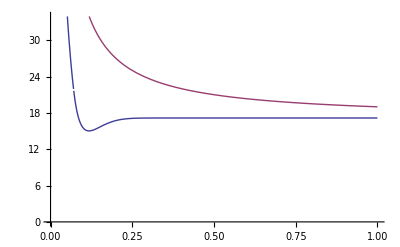

```mathematica
Plot[{normd2f[a,h]/normdf[a,h],tau[h]},{h,0,1},AxesOrigin->{0,0}]
```

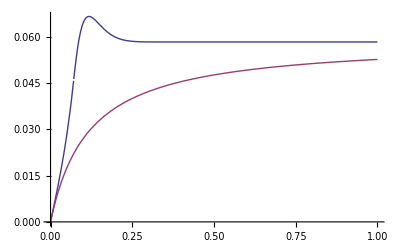

```mathematica
Plot[{normdf[a,h]/normd2f[a,h],1./tau[h]},{h,0,1},AxesOrigin->{0,0}]
```

```mathematica
Integrate[p x^(p-1),{x,0,h}]/Integrate[x^p,{x,0,h}]
```

ConditionalExpression[(1+p)/h,Re[p]>0]